```mathematica
s3.s1.s4.s3.s1.s2.s5.s4//MatrixForm
```

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | -1
-1/2 | -1/2 | 0 | 1 | 0
1/2 | -1/2 | 0 | 0 | 0
1/2 | 1/2 | -1 | 0 | 0)

```mathematica
MemberQ[matrices,({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}})]
```

False

```mathematica
count=0;(aux=NestWhile[(Print[count++];

Union[#~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#,1],1]])&,{IdentityMatrix[5]},! MemberQ[#,({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}})]&,2,50])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

{4.15377,1731}

```mathematica
PauliMatrix[5]
```

PauliMatrix[5]

```mathematica
count=0;Nest[(Print[count++];

 Union[#~Join~Flatten[Outer[Dot,{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]},#,1],1]])&,{IdentityMatrix[2]},2]
```

0

1

{{{0,-1},{1,0}},{{0,-ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,ⅈ},{ⅈ,0}},{{0,1},{-1,0}},{{0,1},{1,0}},{{-ⅈ,0},{0,ⅈ}},{{ⅈ,0},{0,-ⅈ}},{{1,0},{0,-1}},{{1,0},{0,1}}}

```mathematica
Clear[a,b,c,d,e]
```

```mathematica
Unprotect[NonCommutativeMultiply];Clear[NonCommutativeMultiply];
```

```mathematica
Unprotect[NonCommutativeMultiply];Clear[NonCommutativeMultiply,word];
word[g___]**word[h___]:=word[g,h];
word[g1___,g_]**word[g_,h2___]:=word[g1,h2];
word[a___,Subscript[g, 1],Subscript[g, 1],b___]:=word[a,b];
word[a___,Subscript[g, 2],Subscript[g, 2],b___]:=word[a,b];
word[a___,Subscript[g, 3],Subscript[g, 3],b___]:=word[a,b];
word[a___,Subscript[g, 4],Subscript[g, 4],b___]:=word[a,b];
word[a___,Subscript[g, 5],Subscript[g, 5],b___]:=word[a,b];
word[a___,Subscript[g, 1],Subscript[g, 2],b___]:=word[a,Subscript[g, 2],Subscript[g, 1],b];
word[a___,Subscript[g, 1],Subscript[g, 4],b___]:=word[a,Subscript[g, 4],Subscript[g, 1],b];
word[a___,Subscript[g, 1],Subscript[g, 5],b___]:=word[a,Subscript[g, 5],Subscript[g, 1],b];
word[a___,Subscript[g, 2],Subscript[g, 4],b___]:=word[a,Subscript[g, 4],Subscript[g, 2],b];
word[a___,Subscript[g, 2],Subscript[g, 5],b___]:=word[a,Subscript[g, 5],Subscript[g, 2],b];
word[a___,Subscript[g, 3],Subscript[g, 5],b___]:=word[a,Subscript[g, 5],Subscript[g, 3],b];
word[a___,Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],b___]:=word[a,b];
word[a___,Subscript[g, 1],Subscript[g, 4],Subscript[g, 1],Subscript[g, 4],b___]:=word[a,b];
word[a___,Subscript[g, 1],Subscript[g, 5],Subscript[g, 1],Subscript[g, 5],b___]:=word[a,b];
word[a___,Subscript[g, 2],Subscript[g, 4],Subscript[g, 2],Subscript[g, 4],b___]:=word[a,b];
word[a___,Subscript[g, 2],Subscript[g, 5],Subscript[g, 2],Subscript[g, 5],b___]:=word[a,b];
word[a___,Subscript[g, 3],Subscript[g, 5],Subscript[g, 3],Subscript[g, 5],b___]:=word[a,b];
word[a___,Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],b___]:=word[a,b];
word[a___,Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],b___]:=word[a,b];
word[a___,Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],b___]:=word[a,b];
word[a___,Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],b___]:=word[a,b];
word[a___,Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],b___]:=word[a,Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],b];
word[a___,Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],b___]:=word[a,Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],b];
word[a___,Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],b___]:=word[a,Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],b];
word[a___,Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],b___]:=word[a,Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],b];
word[a___,Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],b___]:=word[a,Subscript[g, 3],Subscript[g, 1],b];
word[a___,Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],b___]:=word[a,Subscript[g, 3],Subscript[g, 2],b];
word[a___,Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],b___]:=word[a,Subscript[g, 4],Subscript[g, 3],b];
word[a___,Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],b___]:=word[a,Subscript[g, 5],Subscript[g, 4],b];
Protect[NonCommutativeMultiply];
twoGroup[generators_List,n_Integer]:=Flatten[NestList[(Flatten[Outer[NonCommutativeMultiply,#,generators]]//Union)&,{word[]},n]]//Union
```

```mathematica
word[a,Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],b,c]**word[c,d]
```

word[a,b,d]

```mathematica
{staro}.g1, {staro}.g2
```

```mathematica
grouplist
```

$Aborted[]

```mathematica
word[Subscript[g, 1],Subscript[g, 2]]/.rep//MatrixForm
word[Subscript[g, 2],Subscript[g, 1]]/.rep//MatrixForm
```

(0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -1)

(0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -1)

```mathematica
Table[If[(a/.rep)==(b/rep)&&a!=b,Print[{a,b}],Nothing],{a,grouplist},{b,grouplist}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
grouplist//Length
grouplist/.rep//DeleteDuplicates//Length
```

116

89

```mathematica
nNN=5;
grouplist=Complement[twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]],word[Subscript[g, 4]],word[Subscript[g, 5]]},nNN],twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]],word[Subscript[g, 4]],word[Subscript[g, 5]]},nNN-1]];//Timing
```

{0.045022,Null}

```mathematica
fourlist = Complement[twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]],word[Subscript[g, 4]],word[Subscript[g, 5]]},4],twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]],word[Subscript[g, 4]],word[Subscript[g, 5]]},4-1]]
```

```mathematica
{,word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 3],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 3],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 3],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 3],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 4],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 4],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 4],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 4],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 4],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 5],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 5],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 3],Subscript[g, 5],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 1],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 1],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 1],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 1],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 2],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 2],Subscript[g, 3]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 2],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 2],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 4]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 5]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 1]],word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 2]],,}
```

```mathematica
word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 4]]/.rep
```

{{1/2,1/2,0,1,0},{1/2,1/2,0,-1,0},{1,0,0,0,0},{-1/2,-1/2,1,0,0},{0,0,0,0,1}}

```mathematica
Subscript[g, 5]/.rep
```

{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,1,0},{-1/2,-1/2,1,0,0},{0,0,0,0,1}}

```mathematica
aword = word[Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]];
Table[If[((element**aword)/.rep)==({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}}),Print[element**aword];Break[];,Nothing],{element,grouplist}]//Timing
(*EmitSound[Sound[SoundNote[]]]*)
```

word[g_3,g_2,g_4,g_3,g_1,g_5,g_4,g_3,g_2,g_5,g_4,g_5,g_3]

Break::nofwd: No enclosing For, While, or Do found for Break[].

Hold[Break[]]

```mathematica
word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]]
```

word[g_3,g_4,g_5,g_2,g_3,g_4,g_5,g_1,g_3,g_4,g_5,g_2,g_3]

```mathematica
Subscript[s, 3] Subscript[s, 4] Subscript[s, 5] Subscript[s, 2] Subscript[s, 3] Subscript[s, 4] Subscript[s, 5] Subscript[s, 1] Subscript[s, 3] Subscript[s, 4] Subscript[s, 5] Subscript[s, 2] Subscript[s, 3]
```

```mathematica
s3.s2.s4.s3.s1.s5.s4.s3.s2.s5.s4.s5.s3//MatrixForm
```

(1/2 | 1/2 | 0 | -1 | 0
1/2 | 1/2 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
-1/2 | -1/2 | 1 | 0 | 0)

```mathematica
word[Subscript[g, 3],Subscript[g, 2],Subscript[g, 4],Subscript[g, 3],Subscript[g, 1],Subscript[g, 5],Subscript[g, 4],Subscript[g, 3],Subscript[g, 2],Subscript[g, 5],Subscript[g, 4],Subscript[g, 5],Subscript[g, 3]]/.rep//MatrixForm
```

(1/2 | 1/2 | 0 | -1 | 0
1/2 | 1/2 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
-1/2 | -1/2 | 1 | 0 | 0)

```mathematica
word[Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2],Subscript[g, 1],Subscript[g, 2]]
```

word[]

```mathematica
a E^(b x)/.fit/.x->11
```

9266.33

{a→0.0000407593,b→1.74927}

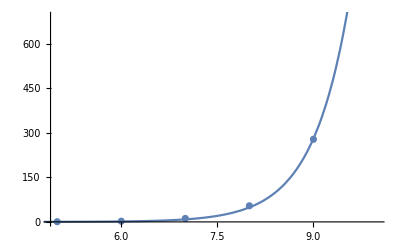

```mathematica
data = {{5,.6},{6,2.418164},{7,11.707672},{8,54.232011},{9,278},{10,1611.62538}};
fit  = FindFit[data,{a E^(b x)},{a,b},x]
Show[ListPlot[data],Plot[a E^(b x)/.fit,{x,1,12}]]
```

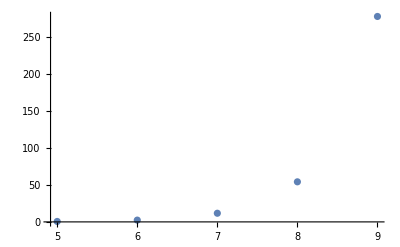

```mathematica
ListPlot[{{5,.6},{6,2.418164},{7,11.707672},{8,54.232011},{9,278}}]
```

```mathematica
twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]],word[Subscript[g, 4]],word[Subscript[g, 5]]},9]//Length
```

428376

```mathematica
Table[twoGroup[{a,b,c,d,e},n]//DeleteDuplicates//Length,{n,0,4}]
```

{1,6,31,156,781}

```mathematica
twoGroup[{word[Subscript[g, 1]],word[Subscript[g, 2]],word[Subscript[g, 3]]},6]
```

{word[],word[g_1],word[g_2],word[g_3],word[g_1,g_2],word[g_1,g_3],word[g_2,g_1],word[g_2,g_3],word[g_3,g_1],word[g_3,g_2],word[g_1,g_2,g_1],word[g_1,g_2,g_3],word[g_1,g_3,g_1],word[g_1,g_3,g_2],word[g_2,g_1,g_2],word[g_2,g_1,g_3],word[g_2,g_3,g_1],word[g_2,g_3,g_2],word[g_3,g_1,g_2],word[g_3,g_1,g_3],word[g_3,g_2,g_1],word[g_3,g_2,g_3],word[g_1,g_2,g_1,g_3],word[g_1,g_2,g_3,g_1],word[g_1,g_2,g_3,g_2],word[g_1,g_3,g_1,g_2],word[g_1,g_3,g_1,g_3],word[g_1,g_3,g_2,g_1],word[g_1,g_3,g_2,g_3],word[g_2,g_1,g_2,g_1],word[g_2,g_1,g_2,g_3],word[g_2,g_1,g_3,g_1],word[g_2,g_1,g_3,g_2],word[g_2,g_3,g_1,g_2],word[g_2,g_3,g_1,g_3],word[g_2,g_3,g_2,g_1],word[g_2,g_3,g_2,g_3],word[g_3,g_1,g_2,g_1],word[g_3,g_1,g_2,g_3],word[g_3,g_1,g_3,g_1],word[g_3,g_1,g_3,g_2],word[g_3,g_2,g_1,g_2],word[g_3,g_2,g_1,g_3],word[g_3,g_2,g_3,g_1],word[g_3,g_2,g_3,g_2],word[g_1,g_2,g_1,g_3,g_1],word[g_1,g_2,g_1,g_3,g_2],word[g_1,g_2,g_3,g_1,g_2],word[g_1,g_2,g_3,g_1,g_3],word[g_1,g_2,g_3,g_2,g_1],word[g_1,g_2,g_3,g_2,g_3],word[g_1,g_3,g_1,g_2,g_1],word[g_1,g_3,g_1,g_2,g_3],word[g_1,g_3,g_1,g_3,g_1],word[g_1,g_3,g_1,g_3,g_2],word[g_1,g_3,g_2,g_1,g_2],word[g_1,g_3,g_2,g_1,g_3],word[g_1,g_3,g_2,g_3,g_1],word[g_1,g_3,g_2,g_3,g_2],word[g_2,g_1,g_2,g_1,g_2],word[g_2,g_1,g_2,g_1,g_3],word[g_2,g_1,g_2,g_3,g_1],word[g_2,g_1,g_2,g_3,g_2],word[g_2,g_1,g_3,g_1,g_2],word[g_2,g_1,g_3,g_1,g_3],word[g_2,g_1,g_3,g_2,g_1],word[g_2,g_1,g_3,g_2,g_3],word[g_2,g_3,g_1,g_2,g_1],word[g_2,g_3,g_1,g_2,g_3],word[g_2,g_3,g_1,g_3,g_1],word[g_2,g_3,g_1,g_3,g_2],word[g_2,g_3,g_2,g_1,g_2],word[g_2,g_3,g_2,g_1,g_3],word[g_2,g_3,g_2,g_3,g_1],word[g_2,g_3,g_2,g_3,g_2],word[g_3,g_1,g_2,g_1,g_2],word[g_3,g_1,g_2,g_1,g_3],word[g_3,g_1,g_2,g_3,g_1],word[g_3,g_1,g_2,g_3,g_2],word[g_3,g_1,g_3,g_1,g_2],word[g_3,g_1,g_3,g_1,g_3],word[g_3,g_1,g_3,g_2,g_1],word[g_3,g_1,g_3,g_2,g_3],word[g_3,g_2,g_1,g_2,g_1],word[g_3,g_2,g_1,g_2,g_3],word[g_3,g_2,g_1,g_3,g_1],word[g_3,g_2,g_1,g_3,g_2],word[g_3,g_2,g_3,g_1,g_2],word[g_3,g_2,g_3,g_1,g_3],word[g_3,g_2,g_3,g_2,g_1],word[g_3,g_2,g_3,g_2,g_3],word[g_1,g_2,g_1,g_3,g_1,g_2],word[g_1,g_2,g_1,g_3,g_1,g_3],word[g_1,g_2,g_1,g_3,g_2,g_1],word[g_1,g_2,g_1,g_3,g_2,g_3],word[g_1,g_2,g_3,g_1,g_2,g_1],word[g_1,g_2,g_3,g_1,g_2,g_3],word[g_1,g_2,g_3,g_1,g_3,g_1],word[g_1,g_2,g_3,g_1,g_3,g_2],word[g_1,g_2,g_3,g_2,g_1,g_2],word[g_1,g_2,g_3,g_2,g_1,g_3],word[g_1,g_2,g_3,g_2,g_3,g_1],word[g_1,g_2,g_3,g_2,g_3,g_2],word[g_1,g_3,g_1,g_2,g_1,g_2],word[g_1,g_3,g_1,g_2,g_1,g_3],word[g_1,g_3,g_1,g_2,g_3,g_1],word[g_1,g_3,g_1,g_2,g_3,g_2],word[g_1,g_3,g_1,g_3,g_1,g_2],word[g_1,g_3,g_1,g_3,g_2,g_1],word[g_1,g_3,g_1,g_3,g_2,g_3],word[g_1,g_3,g_2,g_1,g_2,g_1],word[g_1,g_3,g_2,g_1,g_2,g_3],word[g_1,g_3,g_2,g_1,g_3,g_1],word[g_1,g_3,g_2,g_1,g_3,g_2],word[g_1,g_3,g_2,g_3,g_1,g_2],word[g_1,g_3,g_2,g_3,g_1,g_3],word[g_1,g_3,g_2,g_3,g_2,g_1],word[g_1,g_3,g_2,g_3,g_2,g_3],word[g_2,g_1,g_2,g_1,g_2,g_1],word[g_2,g_1,g_2,g_1,g_2,g_3],word[g_2,g_1,g_2,g_1,g_3,g_1],word[g_2,g_1,g_2,g_1,g_3,g_2],word[g_2,g_1,g_2,g_3,g_1,g_2],word[g_2,g_1,g_2,g_3,g_1,g_3],word[g_2,g_1,g_2,g_3,g_2,g_1],word[g_2,g_1,g_2,g_3,g_2,g_3],word[g_2,g_1,g_3,g_1,g_2,g_1],word[g_2,g_1,g_3,g_1,g_2,g_3],word[g_2,g_1,g_3,g_1,g_3,g_1],word[g_2,g_1,g_3,g_1,g_3,g_2],word[g_2,g_1,g_3,g_2,g_1,g_2],word[g_2,g_1,g_3,g_2,g_1,g_3],word[g_2,g_1,g_3,g_2,g_3,g_1],word[g_2,g_1,g_3,g_2,g_3,g_2],word[g_2,g_3,g_1,g_2,g_1,g_2],word[g_2,g_3,g_1,g_2,g_1,g_3],word[g_2,g_3,g_1,g_2,g_3,g_1],word[g_2,g_3,g_1,g_2,g_3,g_2],word[g_2,g_3,g_1,g_3,g_1,g_2],word[g_2,g_3,g_1,g_3,g_1,g_3],word[g_2,g_3,g_1,g_3,g_2,g_1],word[g_2,g_3,g_1,g_3,g_2,g_3],word[g_2,g_3,g_2,g_1,g_2,g_1],word[g_2,g_3,g_2,g_1,g_2,g_3],word[g_2,g_3,g_2,g_1,g_3,g_1],word[g_2,g_3,g_2,g_1,g_3,g_2],word[g_2,g_3,g_2,g_3,g_1,g_2],word[g_2,g_3,g_2,g_3,g_1,g_3],word[g_2,g_3,g_2,g_3,g_2,g_1],word[g_3,g_1,g_2,g_1,g_2,g_1],word[g_3,g_1,g_2,g_1,g_2,g_3],word[g_3,g_1,g_2,g_1,g_3,g_1],word[g_3,g_1,g_2,g_1,g_3,g_2],word[g_3,g_1,g_2,g_3,g_1,g_2],word[g_3,g_1,g_2,g_3,g_1,g_3],word[g_3,g_1,g_2,g_3,g_2,g_1],word[g_3,g_1,g_2,g_3,g_2,g_3],word[g_3,g_1,g_3,g_1,g_2,g_1],word[g_3,g_1,g_3,g_1,g_2,g_3],word[g_3,g_1,g_3,g_1,g_3,g_1],word[g_3,g_1,g_3,g_1,g_3,g_2],word[g_3,g_1,g_3,g_2,g_1,g_2],word[g_3,g_1,g_3,g_2,g_1,g_3],word[g_3,g_1,g_3,g_2,g_3,g_1],word[g_3,g_1,g_3,g_2,g_3,g_2],word[g_3,g_2,g_1,g_2,g_1,g_2],word[g_3,g_2,g_1,g_2,g_1,g_3],word[g_3,g_2,g_1,g_2,g_3,g_1],word[g_3,g_2,g_1,g_2,g_3,g_2],word[g_3,g_2,g_1,g_3,g_1,g_2],word[g_3,g_2,g_1,g_3,g_1,g_3],word[g_3,g_2,g_1,g_3,g_2,g_1],word[g_3,g_2,g_1,g_3,g_2,g_3],word[g_3,g_2,g_3,g_1,g_2,g_1],word[g_3,g_2,g_3,g_1,g_2,g_3],word[g_3,g_2,g_3,g_1,g_3,g_1],word[g_3,g_2,g_3,g_1,g_3,g_2],word[g_3,g_2,g_3,g_2,g_1,g_2],word[g_3,g_2,g_3,g_2,g_1,g_3],word[g_3,g_2,g_3,g_2,g_3,g_1],word[g_3,g_2,g_3,g_2,g_3,g_2]}

```mathematica
word
```

```mathematica
word[Subscript[g, 1],Subscript[g, 5]]**word[Subscript[g, 1],Subscript[g, 5]]
```

word[]

```mathematica
rep = {Subscript[g, 1] -> s1, 
   Subscript[g, 2] -> s2, 
   Subscript[g, 3] -> s3,
Subscript[g, 4] -> s4,
Subscript[g, 5] -> s5, 
   word[] -> IdentityMatrix[5], word -> Dot};
```

```mathematica
twoGroup[rep]
```

twoGroup[{g_1→{{-1,2,2},{0,1,0},{0,0,1}},g_2→{{1,0,0},{2,-1,2},{0,0,1}},g_3→{{1,0,0},{0,1,0},{2,2,-1}},word[]→{{1,0,0},{0,1,0},{0,0,1}},word→Dot}]

```mathematica
union
```

{{{-1,0},{0,1}},{{0,-1},{-1,0}},{{0,-1},{1,0}},{{0,-ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,ⅈ},{-ⅈ,0}},{{0,ⅈ},{ⅈ,0}},{{0,1},{-1,0}},{{0,1},{1,0}},{{-ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}},{{ⅈ,0},{0,-ⅈ}},{{ⅈ,0},{0,ⅈ}},{{1,0},{0,-1}},{{1,0},{0,1}}}

```mathematica
count=0;(aux=NestWhile[(Print[count++];

Union[#~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#,1],1]])&,{({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}})},! MemberQ[#,IdentityMatrix[5]]&,2,50])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

{4.12063,1731}

```mathematica
matrices//Length
```

1920

```mathematica
MatrixPower[({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}}),2]
```

{{1/2,1/2,0,0,-1},{1/2,1/2,0,0,1},{1/2,1/2,0,1,0},{-1/2,-1/2,1,0,0},{-1/2,1/2,0,0,0}}

```mathematica
Table[MatrixPower[({{1/2, 1/2, 0, -1, 0}, {1/2, 1/2, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}}),n],{n,8,8}]
```

{{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}}

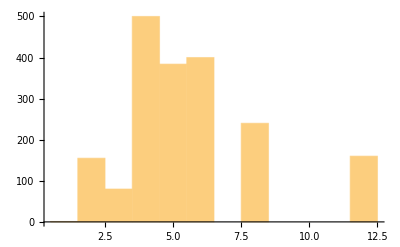

```mathematica
matrixOrder[a_,maxIter_:9999]:=Module[{n=1,i=IdentityMatrix[Length[a]]},NestWhile[(n++;a.#)&,a,!And@@(PossibleZeroQ/@Flatten[#-i])&,1,maxIter];n];
Histogram[matrixOrder/@matrices,{1/2,25/2,1}]
```

```mathematica
StringJoin@MapThread[ConstantArray,{char,#}]&/@f[13,{5,5,5,5,5}]
```

{cccdddddeeeee,ccccddddeeeee,ccccdddddeeee,cccccdddeeeee,cccccddddeeee,cccccdddddeee,bccdddddeeeee,bcccddddeeeee,bcccdddddeeee,bccccdddeeeee,bccccddddeeee,bccccdddddeee,bcccccddeeeee,bcccccdddeeee,bcccccddddeee,bcccccdddddee,bbcdddddeeeee,bbccddddeeeee,bbccdddddeeee,bbcccdddeeeee,bbcccddddeeee,bbcccdddddeee,bbccccddeeeee,bbccccdddeeee,bbccccddddeee,bbccccdddddee,bbcccccdeeeee,bbcccccddeeee,bbcccccdddeee,bbcccccddddee,bbcccccddddde,bbbdddddeeeee,bbbcddddeeeee,bbbcdddddeeee,bbbccdddeeeee,bbbccddddeeee,bbbccdddddeee,bbbcccddeeeee,bbbcccdddeeee,bbbcccddddeee,bbbcccdddddee,bbbccccdeeeee,bbbccccddeeee,bbbccccdddeee,bbbccccddddee,bbbccccddddde,bbbccccceeeee,bbbcccccdeeee,bbbcccccddeee,bbbcccccdddee,bbbcccccdddde,bbbcccccddddd,bbbbddddeeeee,bbbbdddddeeee,bbbbcdddeeeee,bbbbcddddeeee,bbbbcdddddeee,bbbbccddeeeee,bbbbccdddeeee,bbbbccddddeee,bbbbccdddddee,bbbbcccdeeeee,bbbbcccddeeee,bbbbcccdddeee,bbbbcccddddee,bbbbcccddddde,bbbbcccceeeee,bbbbccccdeeee,bbbbccccddeee,bbbbccccdddee,bbbbccccdddde,bbbbccccddddd,bbbbccccceeee,bbbbcccccdeee,bbbbcccccddee,bbbbcccccddde,bbbbcccccdddd,bbbbbdddeeeee,bbbbbddddeeee,bbbbbdddddeee,bbbbbcddeeeee,bbbbbcdddeeee,bbbbbcddddeee,bbbbbcdddddee,bbbbbccdeeeee,bbbbbccddeeee,bbbbbccdddeee,bbbbbccddddee,bbbbbccddddde,bbbbbccceeeee,bbbbbcccdeeee,bbbbbcccddeee,bbbbbcccdddee,bbbbbcccdddde,bbbbbcccddddd,bbbbbcccceeee,bbbbbccccdeee,bbbbbccccddee,bbbbbccccddde,bbbbbccccdddd,bbbbbccccceee,bbbbbcccccdee,bbbbbcccccdde,bbbbbcccccddd,accdddddeeeee,acccddddeeeee,acccdddddeeee,accccdddeeeee,accccddddeeee,accccdddddeee,acccccddeeeee,acccccdddeeee,acccccddddeee,acccccdddddee,abcdddddeeeee,abccddddeeeee,abccdddddeeee,abcccdddeeeee,abcccddddeeee,abcccdddddeee,abccccddeeeee,abccccdddeeee,abccccddddeee,abccccdddddee,abcccccdeeeee,abcccccddeeee,abcccccdddeee,abcccccddddee,abcccccddddde,abbdddddeeeee,abbcddddeeeee,abbcdddddeeee,abbccdddeeeee,abbccddddeeee,abbccdddddeee,abbcccddeeeee,abbcccdddeeee,abbcccddddeee,abbcccdddddee,abbccccdeeeee,abbccccddeeee,abbccccdddeee,abbccccddddee,abbccccddddde,abbccccceeeee,abbcccccdeeee,abbcccccddeee,abbcccccdddee,abbcccccdddde,abbcccccddddd,abbbddddeeeee,abbbdddddeeee,abbbcdddeeeee,abbbcddddeeee,abbbcdddddeee,abbbccddeeeee,abbbccdddeeee,abbbccddddeee,abbbccdddddee,abbbcccdeeeee,abbbcccddeeee,abbbcccdddeee,abbbcccddddee,abbbcccddddde,abbbcccceeeee,abbbccccdeeee,abbbccccddeee,abbbccccdddee,abbbccccdddde,abbbccccddddd,abbbccccceeee,abbbcccccdeee,abbbcccccddee,abbbcccccddde,abbbcccccdddd,abbbbdddeeeee,abbbbddddeeee,abbbbdddddeee,abbbbcddeeeee,abbbbcdddeeee,abbbbcddddeee,abbbbcdddddee,abbbbccdeeeee,abbbbccddeeee,abbbbccdddeee,abbbbccddddee,abbbbccddddde,abbbbccceeeee,abbbbcccdeeee,abbbbcccddeee,abbbbcccdddee,abbbbcccdddde,abbbbcccddddd,abbbbcccceeee,abbbbccccdeee,abbbbccccddee,abbbbccccddde,abbbbccccdddd,abbbbccccceee,abbbbcccccdee,abbbbcccccdde,abbbbcccccddd,abbbbbddeeeee,abbbbbdddeeee,abbbbbddddeee,abbbbbdddddee,abbbbbcdeeeee,abbbbbcddeeee,abbbbbcdddeee,abbbbbcddddee,abbbbbcddddde,abbbbbcceeeee,abbbbbccdeeee,abbbbbccddeee,abbbbbccdddee,abbbbbccdddde,abbbbbccddddd,abbbbbccceeee,abbbbbcccdeee,abbbbbcccddee,abbbbbcccddde,abbbbbcccdddd,abbbbbcccceee,abbbbbccccdee,abbbbbccccdde,abbbbbccccddd,abbbbbcccccee,abbbbbcccccde,abbbbbcccccdd,aacdddddeeeee,aaccddddeeeee,aaccdddddeeee,aacccdddeeeee,aacccddddeeee,aacccdddddeee,aaccccddeeeee,aaccccdddeeee,aaccccddddeee,aaccccdddddee,aacccccdeeeee,aacccccddeeee,aacccccdddeee,aacccccddddee,aacccccddddde,aabdddddeeeee,aabcddddeeeee,aabcdddddeeee,aabccdddeeeee,aabccddddeeee,aabccdddddeee,aabcccddeeeee,aabcccdddeeee,aabcccddddeee,aabcccdddddee,aabccccdeeeee,aabccccddeeee,aabccccdddeee,aabccccddddee,aabccccddddde,aabccccceeeee,aabcccccdeeee,aabcccccddeee,aabcccccdddee,aabcccccdddde,aabcccccddddd,aabbddddeeeee,aabbdddddeeee,aabbcdddeeeee,aabbcddddeeee,aabbcdddddeee,aabbccddeeeee,aabbccdddeeee,aabbccddddeee,aabbccdddddee,aabbcccdeeeee,aabbcccddeeee,aabbcccdddeee,aabbcccddddee,aabbcccddddde,aabbcccceeeee,aabbccccdeeee,aabbccccddeee,aabbccccdddee,aabbccccdddde,aabbccccddddd,aabbccccceeee,aabbcccccdeee,aabbcccccddee,aabbcccccddde,aabbcccccdddd,aabbbdddeeeee,aabbbddddeeee,aabbbdddddeee,aabbbcddeeeee,aabbbcdddeeee,aabbbcddddeee,aabbbcdddddee,aabbbccdeeeee,aabbbccddeeee,aabbbccdddeee,aabbbccddddee,aabbbccddddde,aabbbccceeeee,aabbbcccdeeee,aabbbcccddeee,aabbbcccdddee,aabbbcccdddde,aabbbcccddddd,aabbbcccceeee,aabbbccccdeee,aabbbccccddee,aabbbccccddde,aabbbccccdddd,aabbbccccceee,aabbbcccccdee,aabbbcccccdde,aabbbcccccddd,aabbbbddeeeee,aabbbbdddeeee,aabbbbddddeee,aabbbbdddddee,aabbbbcdeeeee,aabbbbcddeeee,aabbbbcdddeee,aabbbbcddddee,aabbbbcddddde,aabbbbcceeeee,aabbbbccdeeee,aabbbbccddeee,aabbbbccdddee,aabbbbccdddde,aabbbbccddddd,aabbbbccceeee,aabbbbcccdeee,aabbbbcccddee,aabbbbcccddde,aabbbbcccdddd,aabbbbcccceee,aabbbbccccdee,aabbbbccccdde,aabbbbccccddd,aabbbbcccccee,aabbbbcccccde,aabbbbcccccdd,aabbbbbdeeeee,aabbbbbddeeee,aabbbbbdddeee,aabbbbbddddee,aabbbbbddddde,aabbbbbceeeee,aabbbbbcdeeee,aabbbbbcddeee,aabbbbbcdddee,aabbbbbcdddde,aabbbbbcddddd,aabbbbbcceeee,aabbbbbccdeee,aabbbbbccddee,aabbbbbccddde,aabbbbbccdddd,aabbbbbccceee,aabbbbbcccdee,aabbbbbcccdde,aabbbbbcccddd,aabbbbbccccee,aabbbbbccccde,aabbbbbccccdd,aabbbbbccccce,aabbbbbcccccd,aaadddddeeeee,aaacddddeeeee,aaacdddddeeee,aaaccdddeeeee,aaaccddddeeee,aaaccdddddeee,aaacccddeeeee,aaacccdddeeee,aaacccddddeee,aaacccdddddee,aaaccccdeeeee,aaaccccddeeee,aaaccccdddeee,aaaccccddddee,aaaccccddddde,aaaccccceeeee,aaacccccdeeee,aaacccccddeee,aaacccccdddee,aaacccccdddde,aaacccccddddd,aaabddddeeeee,aaabdddddeeee,aaabcdddeeeee,aaabcddddeeee,aaabcdddddeee,aaabccddeeeee,aaabccdddeeee,aaabccddddeee,aaabccdddddee,aaabcccdeeeee,aaabcccddeeee,aaabcccdddeee,aaabcccddddee,aaabcccddddde,aaabcccceeeee,aaabccccdeeee,aaabccccddeee,aaabccccdddee,aaabccccdddde,aaabccccddddd,aaabccccceeee,aaabcccccdeee,aaabcccccddee,aaabcccccddde,aaabcccccdddd,aaabbdddeeeee,aaabbddddeeee,aaabbdddddeee,aaabbcddeeeee,aaabbcdddeeee,aaabbcddddeee,aaabbcdddddee,aaabbccdeeeee,aaabbccddeeee,aaabbccdddeee,aaabbccddddee,aaabbccddddde,aaabbccceeeee,aaabbcccdeeee,aaabbcccddeee,aaabbcccdddee,aaabbcccdddde,aaabbcccddddd,aaabbcccceeee,aaabbccccdeee,aaabbccccddee,aaabbccccddde,aaabbccccdddd,aaabbccccceee,aaabbcccccdee,aaabbcccccdde,aaabbcccccddd,aaabbbddeeeee,aaabbbdddeeee,aaabbbddddeee,aaabbbdddddee,aaabbbcdeeeee,aaabbbcddeeee,aaabbbcdddeee,aaabbbcddddee,aaabbbcddddde,aaabbbcceeeee,aaabbbccdeeee,aaabbbccddeee,aaabbbccdddee,aaabbbccdddde,aaabbbccddddd,aaabbbccceeee,aaabbbcccdeee,aaabbbcccddee,aaabbbcccddde,aaabbbcccdddd,aaabbbcccceee,aaabbbccccdee,aaabbbccccdde,aaabbbccccddd,aaabbbcccccee,aaabbbcccccde,aaabbbcccccdd,aaabbbbdeeeee,aaabbbbddeeee,aaabbbbdddeee,aaabbbbddddee,aaabbbbddddde,aaabbbbceeeee,aaabbbbcdeeee,aaabbbbcddeee,aaabbbbcdddee,aaabbbbcdddde,aaabbbbcddddd,aaabbbbcceeee,aaabbbbccdeee,aaabbbbccddee,aaabbbbccddde,aaabbbbccdddd,aaabbbbccceee,aaabbbbcccdee,aaabbbbcccdde,aaabbbbcccddd,aaabbbbccccee,aaabbbbccccde,aaabbbbccccdd,aaabbbbccccce,aaabbbbcccccd,aaabbbbbeeeee,aaabbbbbdeeee,aaabbbbbddeee,aaabbbbbdddee,aaabbbbbdddde,aaabbbbbddddd,aaabbbbbceeee,aaabbbbbcdeee,aaabbbbbcddee,aaabbbbbcddde,aaabbbbbcdddd,aaabbbbbcceee,aaabbbbbccdee,aaabbbbbccdde,aaabbbbbccddd,aaabbbbbcccee,aaabbbbbcccde,aaabbbbbcccdd,aaabbbbbcccce,aaabbbbbccccd,aaabbbbbccccc,aaaaddddeeeee,aaaadddddeeee,aaaacdddeeeee,aaaacddddeeee,aaaacdddddeee,aaaaccddeeeee,aaaaccdddeeee,aaaaccddddeee,aaaaccdddddee,aaaacccdeeeee,aaaacccddeeee,aaaacccdddeee,aaaacccddddee,aaaacccddddde,aaaacccceeeee,aaaaccccdeeee,aaaaccccddeee,aaaaccccdddee,aaaaccccdddde,aaaaccccddddd,aaaaccccceeee,aaaacccccdeee,aaaacccccddee,aaaacccccddde,aaaacccccdddd,aaaabdddeeeee,aaaabddddeeee,aaaabdddddeee,aaaabcddeeeee,aaaabcdddeeee,aaaabcddddeee,aaaabcdddddee,aaaabccdeeeee,aaaabccddeeee,aaaabccdddeee,aaaabccddddee,aaaabccddddde,aaaabccceeeee,aaaabcccdeeee,aaaabcccddeee,aaaabcccdddee,aaaabcccdddde,aaaabcccddddd,aaaabcccceeee,aaaabccccdeee,aaaabccccddee,aaaabccccddde,aaaabccccdddd,aaaabccccceee,aaaabcccccdee,aaaabcccccdde,aaaabcccccddd,aaaabbddeeeee,aaaabbdddeeee,aaaabbddddeee,aaaabbdddddee,aaaabbcdeeeee,aaaabbcddeeee,aaaabbcdddeee,aaaabbcddddee,aaaabbcddddde,aaaabbcceeeee,aaaabbccdeeee,aaaabbccddeee,aaaabbccdddee,aaaabbccdddde,aaaabbccddddd,aaaabbccceeee,aaaabbcccdeee,aaaabbcccddee,aaaabbcccddde,aaaabbcccdddd,aaaabbcccceee,aaaabbccccdee,aaaabbccccdde,aaaabbccccddd,aaaabbcccccee,aaaabbcccccde,aaaabbcccccdd,aaaabbbdeeeee,aaaabbbddeeee,aaaabbbdddeee,aaaabbbddddee,aaaabbbddddde,aaaabbbceeeee,aaaabbbcdeeee,aaaabbbcddeee,aaaabbbcdddee,aaaabbbcdddde,aaaabbbcddddd,aaaabbbcceeee,aaaabbbccdeee,aaaabbbccddee,aaaabbbccddde,aaaabbbccdddd,aaaabbbccceee,aaaabbbcccdee,aaaabbbcccdde,aaaabbbcccddd,aaaabbbccccee,aaaabbbccccde,aaaabbbccccdd,aaaabbbccccce,aaaabbbcccccd,aaaabbbbeeeee,aaaabbbbdeeee,aaaabbbbddeee,aaaabbbbdddee,aaaabbbbdddde,aaaabbbbddddd,aaaabbbbceeee,aaaabbbbcdeee,aaaabbbbcddee,aaaabbbbcddde,aaaabbbbcdddd,aaaabbbbcceee,aaaabbbbccdee,aaaabbbbccdde,aaaabbbbccddd,aaaabbbbcccee,aaaabbbbcccde,aaaabbbbcccdd,aaaabbbbcccce,aaaabbbbccccd,aaaabbbbccccc,aaaabbbbbeeee,aaaabbbbbdeee,aaaabbbbbddee,aaaabbbbbddde,aaaabbbbbdddd,aaaabbbbbceee,aaaabbbbbcdee,aaaabbbbbcdde,aaaabbbbbcddd,aaaabbbbbccee,aaaabbbbbccde,aaaabbbbbccdd,aaaabbbbbccce,aaaabbbbbcccd,aaaabbbbbcccc,aaaaadddeeeee,aaaaaddddeeee,aaaaadddddeee,aaaaacddeeeee,aaaaacdddeeee,aaaaacddddeee,aaaaacdddddee,aaaaaccdeeeee,aaaaaccddeeee,aaaaaccdddeee,aaaaaccddddee,aaaaaccddddde,aaaaaccceeeee,aaaaacccdeeee,aaaaacccddeee,aaaaacccdddee,aaaaacccdddde,aaaaacccddddd,aaaaacccceeee,aaaaaccccdeee,aaaaaccccddee,aaaaaccccddde,aaaaaccccdddd,aaaaaccccceee,aaaaacccccdee,aaaaacccccdde,aaaaacccccddd,aaaaabddeeeee,aaaaabdddeeee,aaaaabddddeee,aaaaabdddddee,aaaaabcdeeeee,aaaaabcddeeee,aaaaabcdddeee,aaaaabcddddee,aaaaabcddddde,aaaaabcceeeee,aaaaabccdeeee,aaaaabccddeee,aaaaabccdddee,aaaaabccdddde,aaaaabccddddd,aaaaabccceeee,aaaaabcccdeee,aaaaabcccddee,aaaaabcccddde,aaaaabcccdddd,aaaaabcccceee,aaaaabccccdee,aaaaabccccdde,aaaaabccccddd,aaaaabcccccee,aaaaabcccccde,aaaaabcccccdd,aaaaabbdeeeee,aaaaabbddeeee,aaaaabbdddeee,aaaaabbddddee,aaaaabbddddde,aaaaabbceeeee,aaaaabbcdeeee,aaaaabbcddeee,aaaaabbcdddee,aaaaabbcdddde,aaaaabbcddddd,aaaaabbcceeee,aaaaabbccdeee,aaaaabbccddee,aaaaabbccddde,aaaaabbccdddd,aaaaabbccceee,aaaaabbcccdee,aaaaabbcccdde,aaaaabbcccddd,aaaaabbccccee,aaaaabbccccde,aaaaabbccccdd,aaaaabbccccce,aaaaabbcccccd,aaaaabbbeeeee,aaaaabbbdeeee,aaaaabbbddeee,aaaaabbbdddee,aaaaabbbdddde,aaaaabbbddddd,aaaaabbbceeee,aaaaabbbcdeee,aaaaabbbcddee,aaaaabbbcddde,aaaaabbbcdddd,aaaaabbbcceee,aaaaabbbccdee,aaaaabbbccdde,aaaaabbbccddd,aaaaabbbcccee,aaaaabbbcccde,aaaaabbbcccdd,aaaaabbbcccce,aaaaabbbccccd,aaaaabbbccccc,aaaaabbbbeeee,aaaaabbbbdeee,aaaaabbbbddee,aaaaabbbbddde,aaaaabbbbdddd,aaaaabbbbceee,aaaaabbbbcdee,aaaaabbbbcdde,aaaaabbbbcddd,aaaaabbbbccee,aaaaabbbbccde,aaaaabbbbccdd,aaaaabbbbccce,aaaaabbbbcccd,aaaaabbbbcccc,aaaaabbbbbeee,aaaaabbbbbdee,aaaaabbbbbdde,aaaaabbbbbddd,aaaaabbbbbcee,aaaaabbbbbcde,aaaaabbbbbcdd,aaaaabbbbbcce,aaaaabbbbbccd,aaaaabbbbbccc}

```mathematica
f[k_, {}, c__] := If[+c == k, {{c}}, {}]

f[k_, {x_, r___}, c___] := Join @@ (f[k, {r}, c, #] & /@ 0~Range~Min[x, k - +c])

char={"a","b","c","d","e"};

StringJoin@MapThread[ConstantArray,{char,#}]&/@f[13,{2,4,3,2,2}]
Inner[#2~Table~{#}&,f[13,{2,4,3,2,2}],char,Join]

Permutations/@%
```

{aabbbbcccddee}

{{a,a,b,b,b,b,c,c,c,d,d,e,e}}

{{{a,a,b,b,b,b,c,c,c,d,d,e,e},{a,a,b,b,b,b,c,c,c,d,e,d,e},5405396,{e,e,d,d,c,c,c,b,b,b,a,b,a},{e,e,d,d,c,c,c,b,b,b,b,a,a}}}
 |  |  |  |

```mathematica
count=0;(aux=NestWhile[(Print[count++];

 union = Union[#~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#,1],1]];
Table[StringReplace[str,{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}],{str,union}])&,{"i"},Length[#2]!=Length[#1]&,2,50])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

$Aborted

```mathematica
union//Length
```

1958116

```mathematica
union
```

{aabacabacai,aabacabacbi,aabacabacdi,aabacabacei,aabacabaci,aabacabadai,aabacabadbi,aabacabadci,aabacabadei,aabacabadi,aabacabaeai,1958094,eedededcedi,eedededcei,eedededci,eedededi,eededei,eededi,eedei,eedi,eei,ei,i}
 |  |  |  |

```mathematica
count=0;(stringlist=NestWhile[(Print[count++];

Union[#~Join~Flatten[Outer[StringJoin,{"s1","s2","s3","s4","s5"},#,1],1]])&,{""},! MemberQ[#,({{-1/2, -1/2, 1, 0, -1}, {-1/2, -1/2, 1, 0, 1}, {-1/2, -1/2, 1, 1, 0}, {1/2, -1/2, 0, 0, 0}, {-1/2, -1/2, 0, 0, 0}})]&,2,50])//Length//Timing
```

0

1

2

3

{0.001535,781}

```mathematica
{{a,b,c,d},{c,d}}[[All,1]]
```

{a,c}

```mathematica
{f1[#[[1]]],f2[#[[2]]],f3[#[[3]]]}&
```

```mathematica
Nest[{f1[#[[1]]],f2[#[[2]]]}&,{x,y},4]
```

{f1[f1[f1[f1[x]]]],f2[f2[f2[f2[y]]]]}

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];

Union[#~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#,1],1]])&,{IdentityMatrix[5]},! (MemberQ[#,({{-1/2, -1/2, 0, 0, -1}, {-1/2, -1/2, 0, 0, 1}, {0, -1, 0, 0, 0}, {0, 0, 0, 1, 0}, {-1/2, -1/2, 1, 0, 0}})])&,2,50])//Length//Timing
```

0

1

2

3

4

{0.126315,189}

```mathematica
Join[{"a"},Outer[StringJoin,{"s1","s2","s3","s4","s5"},{"a"},1]]
```

{a,{s1a},{s2a},{s3a},{s4a},{s5a}}

```mathematica
Nest[
Table[StringReplace[str,{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}],]Union[#~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#,1],1]]&

,{"i"},2]
```

{aai,abi,aci,adi,aei,ai,bai,bbi,bci,bdi,bei,bi,cai,cbi,cci,cdi,cei,ci,dai,dbi,dci,ddi,dei,di,eai,ebi,eci,edi,eei,ei,i}

```mathematica
Nest[
( union = Union[#~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#,1],1]];
Table[StringReplace[str,{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}],{str,union}])&

,{"i"},4]
```

{bai,bci,bdi,bei,bi,cai,cbi,cdi,cei,ci,dai,dbi,dci,dei,di,eai,ebi,eci,edi,ei,i,i,abaci,abadi,abaei,abai,abcai,abcbi,abcdi,abcei,abci,abdai,abdbi,abdci,abdei,abdi,abeai,abebi,abeci,abedi,abei,abi,acabi,acaci,acadi,acaei,acai,acbai,acbci,acbdi,acbei,acbi,acdai,acdbi,acdci,acdei,acdi,aceai,acebi,aceci,acedi,acei,aci,adabi,adaci,i,adaei,adai,adbai,adbci,adbdi,adbei,adbi,adcai,adcbi,adcdi,adcei,adci,adeai,adebi,adeci,adedi,adei,adi,aeabi,aeaci,aeadi,i,aeai,aebai,aebci,aebdi,aebei,aebi,aecai,aecbi,aecdi,aecei,aeci,aedai,aedbi,aedci,aedei,aedi,aei,ai,babai,babci,babdi,babei,babi,bacai,bacbi,bacdi,bacei,baci,badai,badbi,badci,badei,badi,baeai,baebi,baeci,baedi,baei,bai,abi,aci,adi,aei,ai,cai,cbi,cdi,cei,ci,dai,dbi,dci,dei,di,eai,ebi,eci,edi,ei,i,bcabi,bcaci,bcadi,bcaei,bcai,bcbai,bcbci,bcbdi,bcbei,bcbi,bcdai,bcdbi,bcdci,bcdei,bcdi,bceai,bcebi,bceci,bcedi,bcei,bci,bdabi,bdaci,bdadi,bdaei,bdai,bdbai,bdbci,i,bdbei,bdbi,bdcai,bdcbi,bdcdi,bdcei,bdci,bdeai,bdebi,bdeci,bdedi,bdei,bdi,beabi,beaci,beadi,beaei,beai,bebai,bebci,bebdi,i,bebi,becai,becbi,becdi,becei,beci,bedai,bedbi,bedci,bedei,bedi,bei,bi,cabai,cabci,cabdi,cabei,cabi,cacai,cacbi,cacdi,cacei,caci,cadai,cadbi,cadci,cadei,cadi,caeai,caebi,caeci,caedi,caei,cai,cbabi,cbaci,cbadi,cbaei,cbai,cbcai,cbcbi,cbcdi,cbcei,cbci,cbdai,cbdbi,cbdci,cbdei,cbdi,cbeai,cbebi,cbeci,cbedi,cbei,cbi,abi,aci,adi,aei,ai,bai,bci,bdi,bei,bi,dai,dbi,dci,dei,di,eai,ebi,eci,edi,ei,i,cdabi,cdaci,cdadi,cdaei,cdai,cdbai,cdbci,cdbdi,cdbei,cdbi,cdcai,cdcbi,cdcdi,cdcei,cdci,cdeai,cdebi,cdeci,cdedi,cdei,cdi,ceabi,ceaci,ceadi,ceaei,ceai,cebai,cebci,cebdi,cebei,cebi,cecai,cecbi,cecdi,i,ceci,cedai,cedbi,cedci,cedei,cedi,cei,ci,dabai,dabci,dabdi,dabei,dabi,dacai,dacbi,dacdi,dacei,daci,dadai,dadbi,dadci,dadei,dadi,daeai,daebi,daeci,daedi,daei,dai,dbabi,dbaci,dbadi,dbaei,dbai,dbcai,dbcbi,dbcdi,dbcei,dbci,dbdai,dbdbi,dbdci,dbdei,dbdi,dbeai,dbebi,dbeci,dbedi,dbei,dbi,dcabi,dcaci,dcadi,dcaei,dcai,dcbai,dcbci,dcbdi,dcbei,dcbi,dcdai,dcdbi,dcdci,dcdei,dcdi,dceai,dcebi,dceci,dcedi,dcei,dci,abi,aci,adi,aei,ai,bai,bci,bdi,bei,bi,cai,cbi,cdi,cei,ci,eai,ebi,eci,edi,ei,i,deabi,deaci,deadi,deaei,deai,debai,debci,debdi,debei,debi,decai,decbi,decdi,decei,deci,dedai,dedbi,dedci,dedei,dedi,dei,di,eabai,eabci,eabdi,eabei,eabi,eacai,eacbi,eacdi,eacei,eaci,eadai,eadbi,eadci,eadei,eadi,eaeai,eaebi,eaeci,eaedi,eaei,eai,ebabi,ebaci,ebadi,ebaei,ebai,ebcai,ebcbi,ebcdi,ebcei,ebci,ebdai,ebdbi,ebdci,ebdei,ebdi,ebeai,ebebi,ebeci,ebedi,ebei,ebi,ecabi,ecaci,ecadi,ecaei,ecai,ecbai,ecbci,ecbdi,ecbei,ecbi,ecdai,ecdbi,ecdci,ecdei,ecdi,eceai,ecebi,ececi,ecedi,ecei,eci,edabi,edaci,edadi,edaei,edai,edbai,edbci,edbdi,edbei,edbi,edcai,edcbi,edcdi,edcei,edci,edeai,edebi,edeci,ededi,edei,edi,abi,aci,adi,aei,ai,bai,bci,bdi,bei,bi,cai,cbi,cdi,cei,ci,dai,dbi,dci,dei,di,i,ei,i}

```mathematica
Nest[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"s1","s2","s3","s4","s5"},#[[2]],1],1]]})&,{IdentityMatrix[5],{"a"}},1]
```

5

{{{-1,-1,-1,0,0},{-1,0,-1,0,0},{-1/2,1/2,-1/2,-1/2,0},{0,0,-1,0,0},{0,0,0,0,-1},{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,1,0,0,0},{0,1,1/2,0,-1/2},{0,1,1/2,0,1/2},{0,1,1,0,0},{1/2,-1/2,-1/2,-1/2,0},{1,-1,0,0,0},{1,0,0,0,0},{1,0,1/2,0,-1/2},{1,0,1/2,0,1/2}},{a,s1a,s2a,s3a,s4a,s5a}}

```mathematica
s1.s2.s3//MatrixForm
```

(0 | 0 | 1 | 0 | 0
1 | 1 | -1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -1)

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];

Union[#~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#,1],1]])&,{"i"},! (count >9)&,2,50])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

{10.9814,12207031}

```mathematica
s1.s3.s1.s3.s1.s3
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
StringReplace["aabbabi",{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}]
```

abi

```mathematica
stringlist = Table[StringReplace[str,{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}],{str,stringlist}];
newstringlist = Table[If[StringLength[str]>9,str,Nothing],{str,stringlist}];
newstringlist//Length
```

$Aborted

$Aborted

1638400

```mathematica
newstringlist//Length
```

1458955

```mathematica
union
```

{aabacabacai,aabacabacbi,aabacabacdi,aabacabacei,aabacabaci,aabacabadai,aabacabadbi,aabacabadci,aabacabadei,aabacabadi,aabacabaeai,1958094,eedededcedi,eedededcei,eedededci,eedededi,eededei,eededi,eedei,eedi,eei,ei,i}
 |  |  |  |

```mathematica
newunion = Table[StringReplace[str,{"aa"..->"","bb"..->"","cc"..->"","dd"..->"","ee"..->"","abab"..->"","adad"..->"","aeae"..->"","bdbd"..->"","bebe"..->"","cece"..->"","acacac"..->"","bcbcbc"..->"","cdcdcd"..->"","dedede"..->""}],{str,union}];
(*newstringlist = Table[If[StringLength[str]>10,str,Nothing],{str,newunion}];*)
```

$Aborted

```mathematica
newstringlist//Length
```

```mathematica
Apply[Dot,(ToExpression[Characters["aabacabacdi"]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})]//MatrixForm
```

(-1/2 | -1/2 | 0 | 0 | 1
-1/2 | -1/2 | 0 | 0 | -1
0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1/2 | 1/2 | -1 | 0 | 0)

```mathematica
Do[
mmat = Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})];
If[mmat==({{-1/2, -1/2, 0, 0, 1}, {-1/2, -1/2, 0, 0, -1}, {0, -1, 0, 0, 0}, {0, 0, 0, 1, 0}, {1/2, 1/2, -1, 0, 0}}),Print[str]; Break[];,Nothing],{str,union}]//Timing
```

aabacabacdi

{0.009956,Null}

```mathematica
Do[
mmat = Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})];
If[mmat==({{-1/2, -1/2, 0, -1, 0}, {-1/2, -1/2, 0, 1, 0}, {0, -1, 0, 0, 0}, {0, 0, 0, 0, 1}, {-1/2, -1/2, 1, 0, 0}}),Print[str]; Break[];,Nothing],{str,newstringlist}]//Timing
```

$Aborted

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#[[2]],1],1]]})&,{{IdentityMatrix[5]},{"i"}},! (count >2)&,2,50])//Length//Timing
Do[
mmat = Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})];
If[mmat==({{1/2, 1/2, 0, 0, -1}, {1/2, 1/2, 0, 0, 1}, {0, 1, 0, 0, 0}, {0, 0, 0, 1, 0}, {-1/2, -1/2, 1, 0, 0}}),Print[str]; Break[];,Nothing],{str,stringlist[[2]]}]
```

0

1

2

{0.020323,2}

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#[[2]],1],1]]})&,{{IdentityMatrix[5]},{"i"}},! (count >4)&,3,50])//Length//Timing
Do[
mmat = Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})];
If[mmat==({{-1/2, -1/2, 0, 0, -1}, {-1/2, -1/2, 0, 0, 1}, {0, -1, 0, 0, 0}, {0, 0, 0, 1, 0}, {-1/2, -1/2, 1, 0, 0}}),Print[str]; Break[];,Nothing],{str,stringlist[[2]]}]//Timing
```

0

1

2

3

4

{0.128218,2}

bcadi

{0.522752,Null}

```mathematica
s2.s3.s1.s4//MatrixForm
```

(-1/2 | -1/2 | 0 | 0 | -1
-1/2 | -1/2 | 0 | 0 | 1
0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
-1/2 | -1/2 | 1 | 0 | 0)

```mathematica
StringLength["cadcabedi"]
```

9

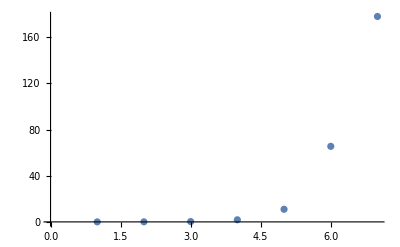

```mathematica
ListPlot[{{1,0.010095},{2,0.055381},{3,0.289983},{4,1.825479},{5,10.942546},{6,65.465262},{7,177.980827}}]
```

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"a","b","c","d","e"},#[[2]],1],1]]})&,{{IdentityMatrix[5]},{"i"}},! (count >7)&,3,50])//Length//Timing
Do[
If[StringLength[str]>=8,If[Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})]==({{-1/2, -1/2, 1, 0, -1}, {-1/2, -1/2, 1, 0, 1}, {-1/2, -1/2, 1, 1, 0}, {1/2, -1/2, 0, 0, 0}, {-1/2, -1/2, 0, 0, 0}}),Print[str]; Break[];,Nothing]],{str,stringlist[[2]]}]//Timing
```

0

1

2

3

4

5

6

7

{1.02082,2}

$Aborted

```mathematica
Apply[Dot,(ToExpression[Characters["abic"]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3})]
```

{{0,0,1,0,0},{1,1,-1,0,0},{0,1,0,0,0},{0,0,0,1,0},{0,0,0,0,-1}}

```mathematica
{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}}.{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}}
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Apply[Dot,{{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}}}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Dot[{{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}}]
```

{{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{1/2,1/2,0,0,1},{0,0,0,1,0},{-1/2,-1/2,1,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}}

```mathematica
Do[
mmat = Apply[Dot,(ToExpression[Characters[str]]/.{i->IdentityMatrix[5],a->s1,b->s2,c->s3,d->s4,e->s5})];
If[mmat==({{-1/2, -1/2, 1, 0, -1}, {-1/2, -1/2, 1, 0, 1}, {-1/2, -1/2, 1, 1, 0}, {1/2, -1/2, 0, 0, 0}, {-1/2, -1/2, 0, 0, 0}}),Print[str],Nothing],{str,stringlist[[2]]}]
```

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"s1","s2","s3","s4","s5"},#[[2]],1],1]]})&,{IdentityMatrix[5],""},! MemberQ[#[[2]],"s5s3s2s1"]&,2,50])//Length//Timing
```

Outer::ipnfm: Positive machine-sized integer or Infinity expected at position 3 in Outer[StringJoin,{s1,s2,s3,s4,s5},,1].

Outer::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

{1.57173,2}

```mathematica
count=0;(stringlist=NestWhile[
(Print[count++];
{Union[#[[1]]~Join~Flatten[Outer[Dot,{s1,s2,s3,s4,s5},#[[1]],1],1]],
Union[#[[2]]~Join~Flatten[Outer[StringJoin,{"s1","s2","s3","s4","s5"},#[[2]],1],1]]})&,{IdentityMatrix[5],""},! MemberQ[#[[2]],"s5s3s2s1"]&,2,50])//Length//Timing
```

```mathematica
Flatten[Outer[StringJoin,{"s1","s2","s3","s4","s5"},"w",1],1]
```

Outer::ipnfm: Positive machine-sized integer or Infinity expected at position 3 in Outer[StringJoin,{s1,s2,s3,s4,s5},w,1].

Outer[StringJoin,{s1,s2,s3,s4,s5},w,1]

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
Outer[StringJoin,{"s1","s2","s3","s4","s5"},{"w"},1]
```

{{s1w},{s2w},{s3w},{s4w},{s5w}}

```mathematica
Outer[Dot,{s1,s2,s3,s4,s5},({{-1/2, -1/2, 1, 0, -1}, {-1/2, -1/2, 1, 0, 1}, {-1/2, -1/2, 1, 1, 0}, {1/2, -1/2, 0, 0, 0}, {-1/2, -1/2, 0, 0, 0}}),1]
```

{{{-1/2,-1/2,-3/2,0,3/2},{-1/2,-1/2,1/2,0,3/2},{-1/2,-1/2,-1/2,1,3/2},{1/2,-1/2,0,0,0},{-1/2,-1/2,-1/2,0,1/2}},{{-1/2,-1/2,1/2,0,-3/2},{-1/2,-1/2,-3/2,0,-3/2},{-1/2,-1/2,-1/2,1,-3/2},{1/2,-1/2,0,0,0},{-1/2,-1/2,-1/2,0,-1/2}},{{1,-2,-1/2,0,-1},{1,-2,-1/2,0,1},{1,-2,-1/2,1,0},{0,0,1/2,0,0},{0,-1,-1/2,0,0}},{{1/2,-1/2,3/2,0,-1},{1/2,-1/2,3/2,0,1},{1/2,-1/2,3/2,1,0},{-1/2,-1/2,-1/2,0,0},{1/2,-1/2,1/2,0,0}},{{0,0,3/2,1/2,-1},{0,0,3/2,1/2,1},{-1,-1,1/2,1/2,0},{1/2,-1/2,0,0,0},{0,0,1/2,1/2,0}}}